```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/biofilm-line.txt",Table[Number,{3}]];
```

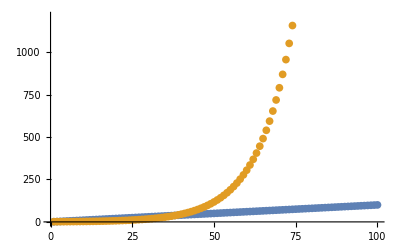

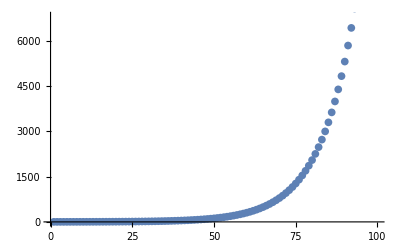

```mathematica
t={};
l={};
For[i=1,i<Length[NT]+1,
AppendTo[t,NT[[i]][[1]]];
AppendTo[l,NT[[i]][[3]]];
i++;
]
ListPlot[{t,l}]
ListPlot[Transpose[{t,l}]]
```

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/spherical-cells/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[current[[1]]];
ni=ToExpression[current[[2]]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
A=Graphics[Circle[{xj,yj},lj]];
AppendTo[plist,A];
j=j+1;
];
rm=20;
pi=Show[{plist},PlotRange->{{-rm,rm},{-rm,rm}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
```

```mathematica
ListAnimate[pl]
```

```mathematica
Export["spherical-expansion.gif",pl]
```

spherical-expansion.gif

```mathematica
pi
```

-Graphics3D-

```mathematica
pl[[1]]
```

-Graphics3D-

```mathematica
pl
```

{}

```mathematica
StringSplit[NT[[1]]]
```

{0,1}

```mathematica
InCyl[x0_,y0_,z0_,a0_,b0_,c0_,x_,y_,z_,L_,R_]:=(
v0={x0,y0,z0};
hv=v0-(L/2)*{a0,b0,c0};
xv={x,y,z};
dv=xv-hv;
rv={a0,b0,c0};
hv2=hv+L*rv;
dv2=xv-hv2;
proj2=dv2.rv;
proj=dv.rv;
norm=Norm[dv]*Sin[ArcCos[dv.rv/Norm[dv]]];
If[(proj>=0&&proj<=L&&norm<=R)||
(proj≤0&&Norm[dv]≤R)||
(proj2≥0&&Norm[dv2]≤R),1,0]
)
```

```mathematica
A=RegionPlot3D[InCyl[0,0,0,1,0,0,x,y,z,1,1]==1,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-16,16}];
B=RegionPlot3D[z<-1&&z>-2,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Brown,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False];
pi=Show[{A,B}]
```

-Graphics3D-

```mathematica
For[jj=0,jj<2+1,Print[jj];jj=jj+1;]
```

0

1

2

```mathematica
ni
```

0

```mathematica
1.76008 0 0 1 0 0 1.768
-1.76008 0 0 1 0 0 1.768
```

```mathematica
A=RegionPlot3D[InCyl[1.13,0,0,1,0,0,x,y,z,2.3,1]==1,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-16,16}];
CC=RegionPlot3D[InCyl[-1.13,0,0,1,0,0,x,y,z,2.3,1]==1,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-16,16}];
B=RegionPlot3D[z<-1&&z>-2,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Brown,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False];
pi=Show[{A,B,CC}]
```

-Graphics3D-

```mathematica
1.13331 0 0 1 0 0 2.26692
-1.13331 0 0 1 0 0 2.26692
```

```mathematica
c
```

```mathematica
ilist=ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/test.txt",String];
plist={};
B=RegionPlot3D[z<-1&&z>-2,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Brown,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False];
For[j=1,j<17,
current=StringSplit[ilist[[j]]];
Print[current];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
A=RegionPlot3D[InCyl[xj,yj,zj,nxj,nyj,nzj,x,y,z,lj,1]==1,{x,-16,16},{y,-4,4},{z,-4,4},Mesh->None,PlotPoints->20,PlotStyle->Directive[Green,Opacity[0.8]],Boxed->False,BoundaryStyle->None,ImageSize->600,Axes->False,PlotRange->{-16,16}];
AppendTo[plist,A];
j=j+1;
];
pi=Show[{plist,B}]
```

{13.8897,0.149864,-0.310885,1,0,0,3.9444}

{9.44716,0.311733,-2.03521,1,0,0,3.9444}

{11.1461,-0.386169,1.37097,1,0,0,3.9444}

{5.83128,-0.531346,1.89017,1,0,0,3.9444}

{5.42868,0.525482,-0.262693,1,0,0,3.9444}

{0.803701,-0.50076,0.774128,1,0,0,3.9444}

{3.8284,0.635017,-2.21614,1,0,0,3.9444}

{-1.35057,0.958101,-3.32445,1,0,0,3.9444}

{1.35179,-0.907861,3.34383,1,0,0,3.9444}

{-3.82996,-0.611087,2.22885,1,0,0,3.9444}

{-0.802316,-0.065813,-0.919346,1,0,0,3.9444}

{-5.44039,0.333144,0.49549,1,0,0,3.9444}

{-5.82149,0.536891,-1.87625,1,0,0,3.9444}

{-11.1471,0.379844,-1.38427,1,0,0,3.9444}

{-9.44697,-0.793393,1.89305,1,0,0,3.9444}

{-13.8841,-0.0296098,0.336755,1,0,0,3.9444}

-Graphics3D-

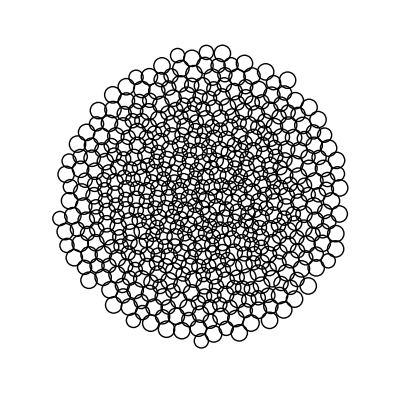

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/spherical-cells/output/test.txt",String];
plist={};
vlist={};
For[j=1,j<ni+1,
current=StringSplit[NT[[j]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
A=Graphics[Circle[{xj,yj},lj]];
AppendTo[plist,A];
j=j+1;
];
rm=20;
pi=Show[{plist},PlotRange->{{-rm,rm},{-rm,rm}}]
```

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[{{12.9251, 1.64728}, {6.03751, 7.52747}, {13.8235, 1.30732}, {10.7199, 4.07071}, {10.654, 4.93598}, {11.8592, 3.33445}, {8.60029, 6.11213}, {1.15247, 10.7116}, {12.5441, 0.93112}, {4.54037, 8.67707}, {8.78294, 8.58172}, {9.86261, 4.2477}, « 27 », {2.48482, 9.8451}, {7.55177, 7.60492}, {4.3945, 7.95216}, {8.18387, 7.17599}, {13.2451, 1.16506}, {5.81695, 7.72668}, {14.0916, 1.21345}, {13.5208, 1.16715}, {11.9317, 2.50287}, {7.19229, 9.79545}, {6.63498, 8.09762}, « 206 »}, Null]. An option must be a rule or a list of rules.

ListPlot[{{12.9251,1.64728},{6.03751,7.52747},{13.8235,1.30732},{10.7199,4.07071},{10.654,4.93598},{11.8592,3.33445},{8.60029,6.11213},{1.15247,10.7116},{12.5441,0.93112},{4.54037,8.67707},{8.78294,8.58172},{9.86261,4.2477},{3.63823,10.6702},{13.2478,1.41676},{13.1713,1.58442},{10.6395,3.22173},{2.23997,8.48967},{5.14222,7.95679},{6.78802,7.54918},{13.1501,1.22572},{13.7235,1.03719},{12.9487,1.35048},{7.59992,6.27472},{4.93992,8.6303},{4.67218,8.02595},{7.73454,7.37201},{12.4345,1.83597},{12.3237,1.95839},{8.71859,6.61491},{13.2852,1.36529},{14.3024,0.909799},{7.60202,8.07758},{9.60259,6.17626},{10.0059,6.10994},{12.9121,0.907169},{12.1247,2.2189},{7.69563,6.37202},{8.34478,9.25667},{9.53171,4.8304},{2.48482,9.8451},{7.55177,7.60492},{4.3945,7.95216},{8.18387,7.17599},{13.2451,1.16506},{5.81695,7.72668},{14.0916,1.21345},{13.5208,1.16715},{11.9317,2.50287},{7.19229,9.79545},{6.63498,8.09762},{6.24244,8.64137},{12.1228,1.92194},{12.3765,2.28502},{10.3777,5.39149},{4.92047,9.47488},{8.01936,7.26187},{12.769,0.806214},{8.99899,7.69749},{7.43089,8.75406},{10.6596,2.71825},{6.27961,8.1802},{11.0719,3.39818},{11.5398,4.43682},{5.83406,7.93567},{12.5168,1.77697},{4.372,9.5607},{13.8184,1.30582},{8.89381,6.19006},{9.77329,6.89796},{9.91565,5.5831},{12.1234,3.43591},{0.421094,10.6785},{10.8269,3.5278},{1.68566,11.1382},{12.0636,3.46075},{11.2104,2.91585},{1.7159,9.6479},{13.6142,1.20997},{13.8717,0.90862},{10.5081,4.10834},{5.13542,8.58767},{7.76488,8.29792},{7.63584,6.696},{10.615,4.2301},{11.4691,3.32814},{11.8105,3.18529},{7.08437,6.76502},{6.42835,7.55083},{4.42507,9.87001},{8.89957,6.15413},{10.9145,5.08495},{13.4065,1.05974},{11.2391,4.12196},{13.675,1.19534},{11.1577,4.72336},{5.83229,8.44217},{9.67838,5.18419},{8.47961,4.50629},{11.802,2.41503},{12.445,2.33533},{10.5967,5.55216},{5.91235,8.88773},{12.8046,1.35893},{3.49285,10.1024},{6.11182,8.63766},{3.07791,10.6685},{7.78438,7.24922},{11.6487,2.75674},{5.36679,8.93682},{9.19349,7.03409},{10.5323,4.68344},{13.0563,1.08015},{9.29938,6.60347},{9.39793,6.29766},{5.97125,5.71969},{13.5784,0.938638},{13.0639,2.25385},{7.43016,6.53657},{3.77875,11.6218},{7.53883,8.94881},{6.22546,8.84839},{7.00282,6.96557},{4.12681,10.7121},{11.0647,4.64347},{3.63564,10.9459},{9.31671,6.06611},{10.8761,3.30068},{4.40027,8.76441},{12.1431,3.35186},{6.9421,10.1663},{12.4363,2.81351},{10.2927,5.18116},{11.4221,3.85479},{10.2368,5.60643},{10.0072,5.54875},{2.85887,9.3186},{11.4199,4.35246},{3.05894,11.2588},{10.091,7.03669},{8.12807,8.21994},{1.93417,11.0871},{11.569,3.35762},{12.6605,3.17072},{9.19642,7.20403},{3.0461,10.3494},{6.44593,9.98794},{7.72898,8.43674},{13.185,1.01487},{11.1414,3.89716},{12.022,3.58311},{8.60287,6.87566},{6.18762,9.62395},{3.78331,9.94076},{7.43014,7.46546},{13.9248,1.02234},{13.2719,1.07278},{8.14596,7.98278},{11.5799,3.83098},{12.6756,2.97673},{6.50338,10.32},{8.90926,8.27977},{10.2947,5.00842},{10.7675,5.5701},{13.3231,1.97693},{9.60115,5.61132},{7.04815,8.26675},{11.1162,5.51234},{2.07888,10.7012},{8.87456,7.86698},{5.21916,10.3365},{9.57703,7.23238},{12.9026,1.68808},{4.45832,10.0333},{13.5417,1.38631},{11.763,4.44675},{10.0203,4.74232},{6.51194,9.26613},{7.51973,7.97895},{5.13981,7.65724},{11.6595,3.44173},{13.9729,1.16767},{8.72975,7.20407},{5.03319,11.3439},{9.35979,5.86},{11.5664,4.29104},{8.14388,9.08981},{7.57062,8.81772},{9.03296,6.83293},{6.02914,9.41841},{11.9764,3.28952},{8.89737,7.07045},{6.29595,8.45212},{9.69358,6.18134},{3.07084,11.6793},{13.4893,1.45155},{8.98781,7.74829},{8.64193,6.19079},{8.68345,8.08028},{11.0671,6.21255},{1.06786,10.3012},{9.9601,7.74083},{1.64336,10.7552},{10.4916,7.17643},{8.90757,7.53888},{3.71504,11.4419},{12.418,3.56024},{14.3656,0.726962},{11.6611,4.77017},{4.85126,10.1535},{5.74318,10.1342},{9.58751,6.27852},{9.32531,8.18693},{13.308,1.16932},{10.8201,5.18528},{7.32508,9.58228},{6.05271,10.51},{2.86051,11.1199},{7.19804,9.19162},{11.3215,5.7773},{10.4321,5.71243},{10.5381,4.42777},{13.1229,0.684349},{8.93615,6.02977},{4.14746,9.58032},{8.46295,7.88901},{7.52474,10.1527},{10.5383,4.46038},{12.2241,3.09828},{8.84307,6.83423},{6.55926,11.2708},{12.8642,2.91782},{3.52622,10.5429},{7.62262,8.21454},{2.92691,10.1949},{6.36859,9.00372},{11.9771,4.55308},{4.13767,11.6701},{10.1003,5.69269},{9.99465,7.69557},{11.2885,5.41182},{10.8247,5.76013},{8.31179,7.11712},{4.95889,10.6312},{13.879,1.14678},{12.3396,2.87726},{6.42786,9.25911},{2.48806,11.5104},{7.42946,8.47872},{5.01602,9.52099},{5.8902,10.2138},{4.93296,10.1979},{9.63766,6.85212},{3.54617,10.8999},{7.70885,8.39418},{8.87348,6.97313},{5.55624,10.9177}},Null]

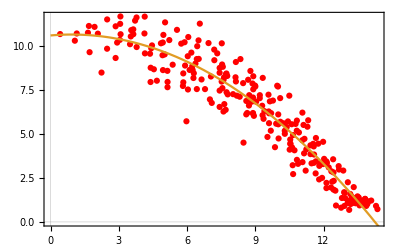

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/spherical-cells/output/test.txt",String];
plist={};
vlist={};
For[j=1,j<256+1,
current=StringSplit[NT[[j]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
AppendTo[plist,xj];
AppendTo[vlist,yj];

j=j+1;
];
data=Transpose[{plist,vlist}];
ListPlot[Transpose[{plist,vlist}],]
parabola=Fit[data,{1,x,x^2},x];
A=Show[ListPlot[data,PlotStyle->Red,PlotTheme->"Scientific",LabelStyle->Large],Plot[{line,parabola},{x,0,15}]]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sphere-pressures.jpg",A]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sphere-pressures.jpg

```mathematica
ilist=ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/test.txt",String];
plist={};
ml=16;
For[j=1,j<9,
current=StringSplit[ilist[[j]]];
Print[current];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];
j=j+1;
];
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,-1}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0,0,3.4},ViewVertical->{0,0,1},PlotRange->{{-ml,ml},{-ml,ml},{-ml,ml}}]
```

{2.24423,1.60001,0,-0.634811,0.772667,0,3.22316}

{0.801173,5.06851,0,-0.737048,0.67584,0,3.22316}

{6.08316,-3.17244,0,0.996887,0.0788465,0,3.22316}

{3.15223,-2.29892,0,-0.981632,-0.190786,0,3.22316}

{-4.45122,-2.64635,0,-0.996432,-0.0843986,0,3.22316}

{-0.741659,-2.21309,0,0.386507,-0.922286,0,3.22316}

{-5.45794,1.82893,0,0.673151,-0.739505,0,3.22316}

{-1.62841,1.83482,0,0.650098,0.75985,0,3.22316}

-Graphics3D-

```mathematica
-Graphics3D-//Options
```

{ImageSize→600,ViewPoint→{0.558283,-3.09873,1.23942},ViewVertical→{0.0348144,-0.327894,1.77708}}

```mathematica
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
```

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/2d-film/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
c=RandomColor[];
(*
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];*)
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2},1]}]];
j=j+1;
];
ml=30;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,-1}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0,0,3.4},ViewVertical->{0,0,1},PlotRange->{{-ml,ml},{-ml,ml},{-ml,ml}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
```

```mathematica
ListAnimate[pl]
```

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
c=RandomColor[];
(*
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];*)
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];
j=j+1;
];
ml=10;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,0}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0,-3.3814094053887342,0.12676427089094683},ViewVertical->{0,-0.6229474303836647,1.4724727983500274},PlotRange->{{-ml,ml},{-ml,ml},{-ml,ml}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
```

```mathematica
ListAnimate[pl]
```

```mathematica
//Options
```

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
c=RandomColor[];
(*
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];*)
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];
j=j+1;
];
ml=30;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,-1}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0.639950568133485,-2.6118371239903477,2.0539644855964445},ViewVertical->{0.0010861326237563249,-0.059167914813952754,1.8790540298850114},PlotRange->{{-ml,ml},{-ml,ml},{-ml,ml}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
```

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/single-cell/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
c=RandomColor[];
(*
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];*)
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[0.8],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2},1]}]];
j=j+1;
];
ml=4;
AppendTo[plist,Graphics3D[{Opacity[0.5],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,0}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0.006855298987010743,-3.3801584222263523,0.1564673944566741},ViewVertical->{-0.001046987906885937,-0.6160521687107411,1.4827381809693596},PlotRange->{{-ml,ml},{-ml,ml},{-2,6}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
ListAnimate[pl]
```

```mathematica
Length[pl]
```

1002

```mathematica
m=ListAnimate[Part[pl,150;;450]]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-horizontal-force.gif",Part[pl,150;;450],"DisplayDurations"->{10/300.}]
```

$Aborted

```mathematica
Length[Take[Part[pl,150;;450],{1,-1,3}]]
```

101

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-horizontal-force.gif",Take[Part[pl,150;;450],{1,-1,3}],"DisplayDurations"->{10/101.}]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-horizontal-force.gif

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-horizontal-force-animate.swf",m]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-horizontal-force-animate.swf

```mathematica
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/output/biofilm-line.txt",String];
tl={};
pl={};
i=0;
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
c=RandomColor[];
(*
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj,yj-nyj*lj,zj-nzj*lj},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj,yj+nyj*lj,zj+nzj*lj},1]}]];*)
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Cylinder[{{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],RGBColor[{0,255,0}],Sphere[{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2},1]}]];
j=j+1;
];
ml=30;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-ml},{ml,ml,0}}]}]];
pi=Show[{plist},ImageSize->600,ViewPoint->{0.558282607530429,-3.0987346923010977,1.2394207666723402},ViewVertical->{0.03481444647067553,-0.32789421737952457,1.7770780969442144},PlotRange->{{-ml,ml},{-ml,ml},{-5,ml}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
ListAnimate[pl]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-3d-colony.gif",Take[Part[pl,150;;450],{1,-1,3}],"DisplayDurations"->{10/101.}]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-3d-colony.gif",Take[pl,{1,-1,7}],"DisplayDurations"->{10/102.}]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-3d-colony.gif

```mathematica
Length[Take[pl,{1,-1,7}]]
```

102

```mathematica
ListAnimate[Take[pl,{1,-1,7}]]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-2d-colony.gif",Take[pl,{1,-1,7}],"DisplayDurations"->{10/103.}]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/1d-film/analysis/plots/sc-2d-colony.gif

```mathematica
Length[pl]
```

718

```mathematica
Length[Take[pl,{1,-1,7}]]
```

103